## Hamiltonians

### Definitions

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with antiperiodic bc *)
ha[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->-tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with e^ik bc *)
hk[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with free bc *)
ω=N [(Sqrt[5]-1)/2];
rot=28; (* rotate the sequence of couplings *)
fib[n_]:=IntegerPart[ω( n+1+rot)]-IntegerPart[ω (n+rot)];
jump[n_,tw_,ts_]:=If[fib[n-1]<1,ts,tw];

hf[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Fibonacci Hamiltonian, in the normal basis, with periodic bc *)
hpn[n_,tw_,ts_]:=Block[{F2=Fibonacci[n+2],tbl,ar},
tbl=Table[{i,i+1}->jump[i,tw,ts],{i,1,F2-1}];
AppendTo[tbl,{1,F2}->tw];
ar=SparseArray[tbl,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* Harper *)
hharp[p_,q_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*periodic boundary conditions*)AppendTo[hopping,{1,q}->-1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.Cos[2 π p i/q],{i,q}],{q,q}];
Normal[pot+hopping]]

(* Harper antiperiodic *)
hharpa[p_,q_]:=Block[{hopping,pot},(*hopping subdiagonal part*)hopping=Table[{i,i+1}->-1.,{i,q-1}];
(*antiperiodic boundary conditions*)AppendTo[hopping,{1,q}->1.];
(*convert to matrix*)hopping=SparseArray[hopping,{q,q}];
(*symmetrize*)hopping=hopping+Transpose[hopping];
(*diagonal part*)pot=SparseArray[Table[{i,i}->2.Cos[2 π p i/q],{i,q}],{q,q}];
Normal[pot+hopping]]

(*choosing Fibonacci numbers as approximants*)
hfib[n_]:=hharp[Fibonacci[n-2],Fibonacci[n-1]];
hfiba[n_]:=hharpa[Fibonacci[n-2],Fibonacci[n-1]];
```

## Average exponents

### Typical x, typical eigenfunction

Let us note Ω^n(x) the number of states having a given value of x at step n. One has
Ω^n(x) = Ω(n_m,n_a) with n_m=n x the number of molecular renormalizations, and n_a=n (1-2x)/3 the number of atomic renormalizations, and
Ω(p,q)=2^p((p+q)!)/(p! q!).
When n becomes large, we have Ω^n(x) ~ F_n^(f(x)) with Log(ϕ)×f(x) = -x Log(3x/2) + (1+x)/3Log(1+x) - (1 - 2x)/3Log(1-2x)

```mathematica
f[x_]:= -x Log[3x/2] + (1+x)/3 Log[1+x] - (1 - 2x)/3 Log[1-2x];
```

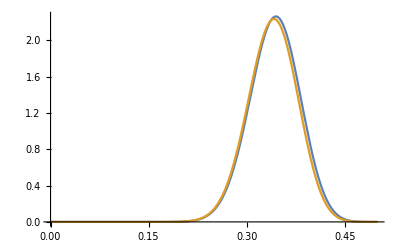

```mathematica
step=100;
compt[x_]:=2^(step x)((step (1+x)/3)!)/((step x)!(step (1-2x)/3)!);
(* the integral does not seem to be accurate... *)
norm=NIntegrate[compt[x],{x,0.,0.5}];
freq[x_]:=compt[x]/norm;
(* compare asymptotic result to exact one *)
Plot[{freq[x]/4.6,Exp[step f[x]]/Fibonacci[step]},{x,0,1/2}]
```

So, the typical value of x is x_0 such that
f'(x_0) = 0

```mathematica
Solve[f'[x]==0,x]
```

{{x→1/5 (-5+3 √5)}}

x_0=2(1-ω^4)/5=2(1-2+3ω)/5=2(3ω-1)/5

### Typical exponent

In the large size limit, almost all wavefunctions have x=x_0. Therefore they have the exponent τ_q(x_0). We also compute the average exponent
χ_q=1/F_n Σ_a χ_q(a) = 1/F_n Σ_x Ω(x) χ_q(x).
Thus, we obtain a relation between the average exponent and the exponent of the typical wavefunction:
τ_q=τ_q(x_0)+1-f(x_0).

```mathematica
(* return bands and intensities ordered by increasing energy *)
IntBands[n_,ρ_]:=IntBands[n,ρ]=Block[{ts=1.,tw=ρ,vpp,vpa,wfp,wfa,o,intensities,intp,inta,bands},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hp[n-2,tw,ts]];
{vpa,wfa}=Eigensystem[ha[n-2,tw,ts]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];

{intensities,bands}]
```

```mathematica
Timing[IntBands[19,0.1];]
```

{226.42,Null}

```mathematica
(* averaged q moment of the intensity *)
avqInt[q_,n_,ρ_]:=avqInt[q,n,ρ]=Total[IntBands[n,ρ][[1]]^q,2]/Fibonacci[n];
```

We expect Log (χ^n)_q ~ -τ_q Log F_n , and indeed, Log (χ^n)_q is a linear function of n ~ Log F_n:

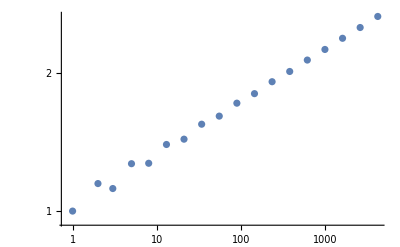

```mathematica
nValues=Range[2,19,1];
avIntN=ParallelMap[avqInt[.8,#,0.1]&,nValues];
ListLogLogPlot[glue[Fibonacci[nValues],avIntN]]
```

For large values of q, the 3-periodic behaviour of the Fibonacci numbers (odd, odd, even...) is clearly visible.
It turns out that when F_n is even, there is a gap at E=0, while there is a band when F_n is odd. Since there is an energy level at E=0 for the quasicrystalline chain, we guess that choosing odd approximant is a better idea. If F_n is odd and F_(n-2) as well, then the 2 lateral clusters have also a band in their center. This is perhaps even better.

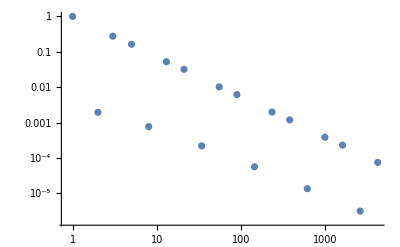

```mathematica
nValues=Range[2,19,1];
avIntN=ParallelMap[avqInt[10.,#,0.1]&,nValues];
ListLogLogPlot[glue[Fibonacci[nValues],avIntN]]
```

For q into the range [0,1) it is safe to disregard the 3-periodicity dependance. Below we compute the slope ie -τ_q for n=13, 16, 19 for different values of q between 0 and 1.

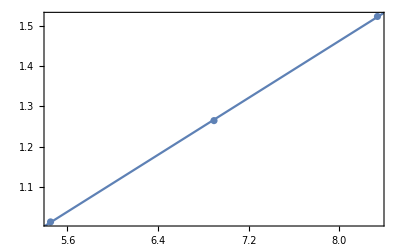

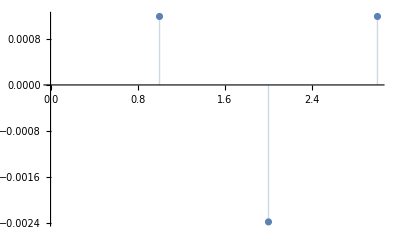

```mathematica
qValues=Range[0,0.9,0.05];
nValues={13,16,19};
avIntN=ParallelMap[avqInt[0.7,#,0.1]&,nValues];

dat=glue[Log[Fibonacci[nValues]],Log[avIntN]];
fit=LinearModelFit[dat,n,n];
Show[ListPlot[dat],Plot[fit[n],{n,0,10}],Frame->True]
ListPlot[fit["FitResiduals"], Filling->Axis]
```

```mathematica
linFit[q_,ρ_,nv_]:=Block[{avIntN,data},
avIntN=ParallelMap[avqInt[q,#,ρ]&,nv];
data=glue[Log[Fibonacci[nv]],Log[avIntN]];
LinearModelFit[data,n,n]
]
```

```mathematica
fits=linFit[#,0.1,nValues]&/@qValues;
```

```mathematica
(* extract Subscript[τ, q]'s from the fits *)
tauqs=-Normal[#["ParameterTable"]][[1,3,2]]&/@fits;
(* convert to Subscript[D, q] *)
dqs=MapThread[#1/(#2-1)&,{tauqs,qValues}];
(* convert to Subscript[Δ, q] *)
Δqs=MapThread[(#1-(#2-1))&,{tauqs,qValues}];
```

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

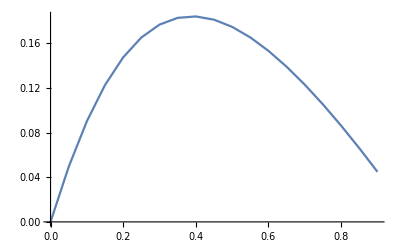

```mathematica
ListPlot[glue[qValues,Δqs],Joined->True]
```

```mathematica
x0=2*(3*ω - 1)/5;
f0=f[x0];
```

```mathematica
0.18+1-f0
```

0.698788

```mathematica
f0
```

0.481212

The 3-periodicity is also visible (although much less apparent) for the Harper model using the golden ratio as the irrational (see subsection below).

### Harper model

```mathematica
(* return bands and intensities ordered by increasing energy *)
IntBandsHarp[n_,ρ_]:=IntBandsHarp[n,ρ]=Block[{ts=1.,tw=ρ,vpp,vpa,wfp,wfa,o,intensities,intp,inta,bands},

(* spectres des systèmes de taille i p et anti-p *)
{vpp,wfp}=Eigensystem[hfib[n]];
{vpa,wfa}=Eigensystem[hfiba[n]];

o=Ordering[vpp];
vpp=vpp[[o]];
wfp=wfp[[o]];
(* intensity *)
intp=Abs[wfp]^2;

o=Ordering[vpa];
vpa=vpa[[o]];
wfa=wfa[[o]];
inta=Abs[wfa]^2;

intensities=0.5*(intp+inta);

(* la taille de la i^ième boîte est la distance entre le niveau i périodique et le niveau i antipériodique *)
bands=MapThread[Abs[#1-#2]&,{vpa,vpp}];

{intensities,bands}]
```

```mathematica
(* averaged q moment of the intensity *)
avqIntHarp[q_,n_,ρ_]:=avqIntHarp[q,n,ρ]=Total[IntBandsHarp[n,ρ][[1]]^q,2]/Fibonacci[n];
```

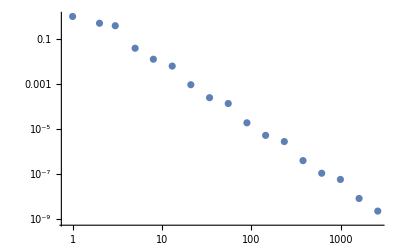

```mathematica
nValues=Range[2,18,1];
avIntN=ParallelMap[avqIntHarp[10.,#,0.1]&,nValues];
ListLogLogPlot[glue[Fibonacci[nValues],avIntN]]
```